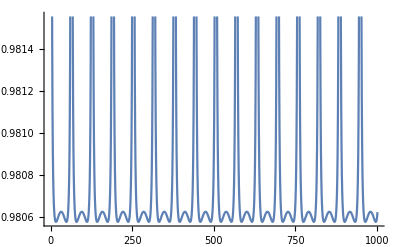

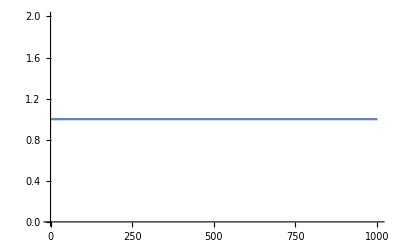

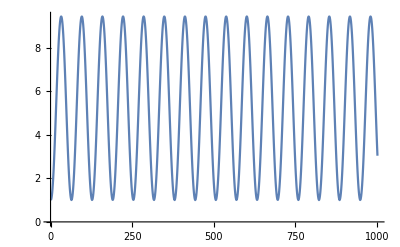

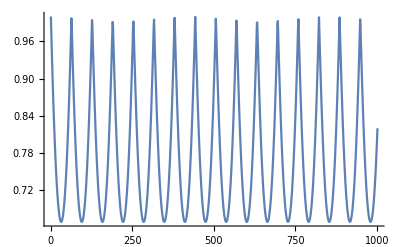

-Graphics-

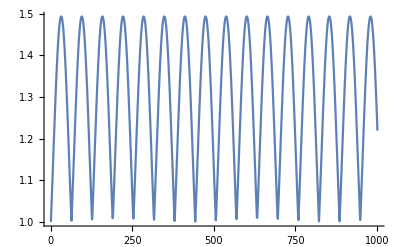

```mathematica
(*X=10 Y=1*)
ListPlot[Table[Eigs[[1]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[Eigs[[2]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[Eigs[[3]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[Eigs[[4]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[Eigs[[5]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[Eigs[[6]],{t,0,10,1/100}],Joined->True]
(*Checking first condition for Bona Fide C.M.; These eigenfunctions should be greater than 0 to be physical*)
```

```mathematica
EigSymp=Eigenvalues[σ+ⅈ Σ];
ListPlot[Table[EigSymp[[1]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[EigSymp[[2]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[EigSymp[[3]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[EigSymp[[4]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[EigSymp[[5]],{t,0,10,1/100}],Joined->True]
ListPlot[Table[EigSymp[[6]],{t,0,10,1/100}],Joined->True]
(*Checking second condition for Bona Fide C.M.; These eigenfunctions should be also greater than 0 to be physical*)
(*NOT PLOTTING*)
```

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

$Aborted

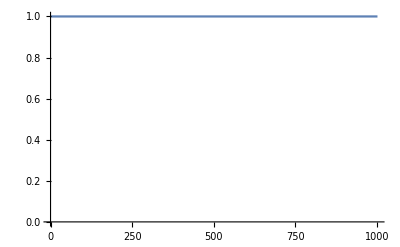

-Graphics-

-Graphics-

-Graphics-

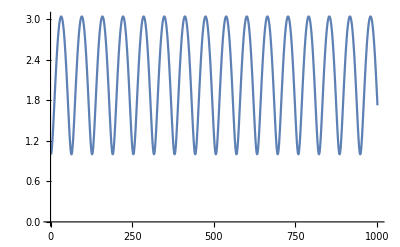

$Aborted

```mathematica
SympEig=Eigenvalues[ⅈ Σ . σ];
ListPlot[Table[Abs[SympEig[[1]]],{t,0,10,1/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[2]]],{t,0,10,1/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[3]]],{t,0,10,1/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[4]]],{t,0,10,1/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[5]]],{t,0,10,1/100}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[6]]],{t,0,10,1/100}],Joined->True,PlotRange->{0,Automatic}]
(*Checking third condition for Bona Fide C.M.; These eigenfunctions should be also greater than or equal 1 (not zero) to be physical*)
```

```mathematica
V1=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]],{t,0,5,1/50}];
V2=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]],{t,0,5,1/50}];
V3=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]],{t,0,5,1/50}];
(*decreased time period and increment as it was taking too long*)
(*Symplectic eigenvalues. If any are less than 1 then there exists some entanglement: NPT criterion*)
```

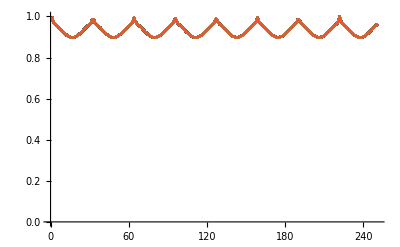

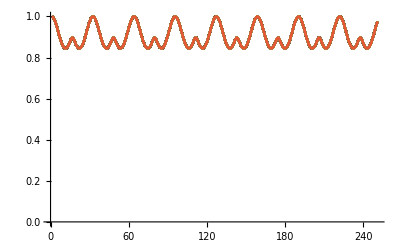

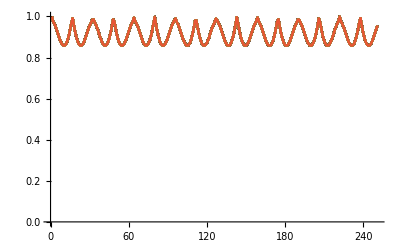

```mathematica
ListPlot[Table[V1,{t,0,5,1/50}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[V2,{t,0,5,1/50}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[V3,{t,0,5,1/50}],Joined->True,PlotRange->{0,Automatic}]
```

```mathematica
LogNeg1=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]],{t,0,5,1/50}];
LogNeg2=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]],{t,0,5,1/50}];
LogNeg3=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]],{t,0,5,1/50}];
```

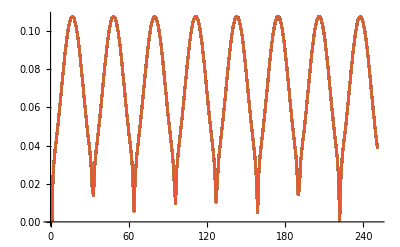

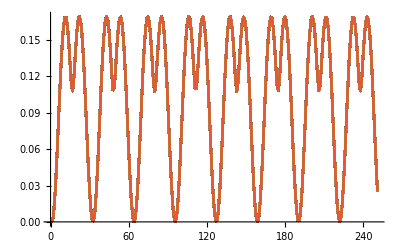

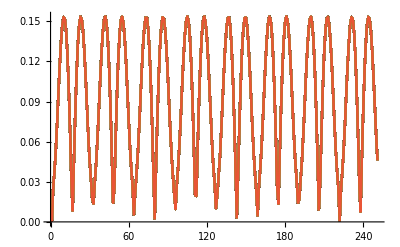

```mathematica
ListPlot[Table[LogNeg1,{t,0,5,1/50}],Joined->True,PlotRange->{0,Automatic}]
(*Min value of entanglement increasing with what looks like a periodic function? MAX was around 0.054*)
ListPlot[Table[LogNeg2,{t,0,5,1/50}],Joined->True,PlotRange->{0,Automatic}]
(*Min value seems to be periodically 0. MAX was around 0.083*)
ListPlot[Table[LogNeg3,{t,0,5,1/50}],Joined->True,PlotRange->{0,Automatic}]
(*Similar to LogNeg1. MAX was around 0.08*)
```

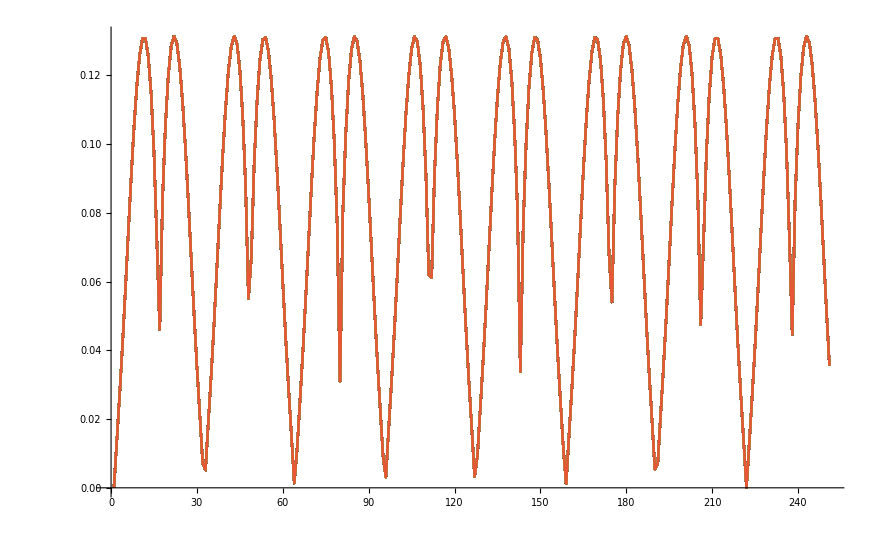

```mathematica
LogNeg123=Table[CubeRoot[(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]])],{t,0,5,1/50}]//Chop;
ListPlot[Table[LogNeg123,{t,0,5,1/50}],Joined->True,PlotRange->{0,Automatic}]
(*MAX Entanglement went from 0.07 for Y=0.5 to 0.13 FOR Y=1*)
```